```mathematica
Quit[]
```

```mathematica
RθkT={{Cos[θk],0,-Sin[θk]},{0,1,0},{Sin[θk],0,Cos[θk]}};RθkT//MatrixForm
RϕkT={{Cos[ϕk],Sin[ϕk],0},{-Sin[ϕk],Cos[ϕk],0},{0,0,1}};RϕkT//MatrixForm
Rϕk=Transpose[RϕkT];Rϕk//MatrixForm
```

(Cos[θk] | 0 | -Sin[θk]
0 | 1 | 0
Sin[θk] | 0 | Cos[θk])

(Cos[ϕk] | Sin[ϕk] | 0
-Sin[ϕk] | Cos[ϕk] | 0
0 | 0 | 1)

(Cos[ϕk] | -Sin[ϕk] | 0
Sin[ϕk] | Cos[ϕk] | 0
0 | 0 | 1)

```mathematica
kk=k Transpose[{{Sin[θk]Cos[ϕk],Sin[θk]Sin[ϕk],Cos[θk]}}];
```

```mathematica
Rϕk.RθkT.RϕkT.kk//Simplify
```

{{0},{0},{k}}

```mathematica
qq=q Transpose[{{0,0,1}}];
qq2=q2 Transpose[{{Sin[θ2]Cos[ϕ2],Sin[θ2]Sin[ϕ2],Cos[θ2]}}];
qq3p=q3p Transpose[{{Sin[θ3p]Cos[ϕ3p],Sin[θ3p]Sin[ϕ3p],Cos[θ3p]}}];
```

```mathematica
qqt=Rϕk.RθkT.RϕkT.qq/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
qq2t=Rϕk.RθkT.RϕkT.qq2/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
qq3pt=Rϕk.RθkT.RϕkT.qq3p/.{Cos[θk]->ck,Sin[θk]->Sqrt[1-ck^2],Cos[θ2]->c2,Sin[θ2]->Sqrt[1-c2^2],Cos[θ3p]->c3p,Sin[θ3p]->Sqrt[1-c3p^2]}//Simplify
```

{{-√(1-ck^2) q Cos[ϕk]},{-√(1-ck^2) q Sin[ϕk]},{ck q}}

{{q2 (-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2))},{q2 (-c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2))},{q2 (c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk])}}

{{q3p (-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2))},{q3p (-c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2))},{q3p (c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk])}}

```mathematica
Flatten[qqt]
```

{-√(1-ck^2) q Cos[ϕk],-√(1-ck^2) q Sin[ϕk],ck q}

```mathematica
xcoord=Join[Flatten[qqt],Flatten[qq2t],Flatten[qq3pt]]
rcoord={q,ck,ϕk,q2,c2,ϕ2,q3p,c3p,ϕ3p}
```

{-√(1-ck^2) q Cos[ϕk],-√(1-ck^2) q Sin[ϕk],ck q,q2 (-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2)),q2 (-c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2)),q2 (c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk]),q3p (-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2)),q3p (-c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2)),q3p (c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk])}

{q,ck,ϕk,q2,c2,ϕ2,q3p,c3p,ϕ3p}

```mathematica
JJ=Table[D[xcoord[[i]], rcoord[[j]]],{i,9},{j,9}]//Simplify
```

{{-√(1-ck^2) Cos[ϕk],(ck q Cos[ϕk])/(√(1-ck^2)),√(1-ck^2) q Sin[ϕk],0,0,0,0,0,0},{-√(1-ck^2) Sin[ϕk],(ck q Sin[ϕk])/(√(1-ck^2)),-√(1-ck^2) q Cos[ϕk],0,0,0,0,0,0},{ck,q,0,0,0,0,0,0,0},{0,q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Cos[ϕk],q2 (√(1-c2^2) (-1+ck) Sin[ϕ2-2 ϕk]+c2 √(1-ck^2) Sin[ϕk]),-c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2),-(q2 (c2 (1+ck) Cos[ϕ2]+c2 (-1+ck) Cos[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c2^2)),-1/2 √(1-c2^2) q2 ((1+ck) Sin[ϕ2]+(-1+ck) Sin[ϕ2-2 ϕk]),0,0,0},{0,q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Sin[ϕk],q2 (√(1-c2^2) (-1+ck) Cos[ϕ2-2 ϕk]-c2 √(1-ck^2) Cos[ϕk]),-c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2),-(q2 (c2 (1+ck) Sin[ϕ2]-c2 (-1+ck) Sin[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c2^2)),1/2 √(1-c2^2) q2 ((1+ck) Cos[ϕ2]-(-1+ck) Cos[ϕ2-2 ϕk]),0,0,0},{0,q2 (c2-(√(1-c2^2) ck Cos[ϕ2-ϕk])/(√(1-ck^2))),√(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk],c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk],q2 (ck-(c2 √(1-ck^2) Cos[ϕ2-ϕk])/(√(1-c2^2))),-√(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk],0,0,0},{0,q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Cos[ϕk],q3p (√(1-c3p^2) (-1+ck) Sin[ϕ3p-2 ϕk]+c3p √(1-ck^2) Sin[ϕk]),0,0,0,-c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2),-(q3p (c3p (1+ck) Cos[ϕ3p]+c3p (-1+ck) Cos[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c3p^2)),-1/2 √(1-c3p^2) q3p ((1+ck) Sin[ϕ3p]+(-1+ck) Sin[ϕ3p-2 ϕk])},{0,q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Sin[ϕk],q3p (√(1-c3p^2) (-1+ck) Cos[ϕ3p-2 ϕk]-c3p √(1-ck^2) Cos[ϕk]),0,0,0,-c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2),-(q3p (c3p (1+ck) Sin[ϕ3p]-c3p (-1+ck) Sin[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c3p^2)),1/2 √(1-c3p^2) q3p ((1+ck) Cos[ϕ3p]-(-1+ck) Cos[ϕ3p-2 ϕk])},{0,q3p (c3p-(√(1-c3p^2) ck Cos[ϕ3p-ϕk])/(√(1-ck^2))),√(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk],0,0,0,c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk],q3p (ck-(c3p √(1-ck^2) Cos[ϕ3p-ϕk])/(√(1-c3p^2))),-√(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk]}}

```mathematica
JJ//MatrixForm
```

(-√(1-ck^2) Cos[ϕk] | (ck q Cos[ϕk])/(√(1-ck^2)) | √(1-ck^2) q Sin[ϕk] | 0 | 0 | 0 | 0 | 0 | 0
-√(1-ck^2) Sin[ϕk] | (ck q Sin[ϕk])/(√(1-ck^2)) | -√(1-ck^2) q Cos[ϕk] | 0 | 0 | 0 | 0 | 0 | 0
ck | q | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Cos[ϕk] | q2 (√(1-c2^2) (-1+ck) Sin[ϕ2-2 ϕk]+c2 √(1-ck^2) Sin[ϕk]) | -c2 √(1-ck^2) Cos[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕk] Sin[ϕ2] Sin[ϕk]+√(1-c2^2) Cos[ϕ2] (ck Cos[ϕk]^2+Sin[ϕk]^2) | -(q2 (c2 (1+ck) Cos[ϕ2]+c2 (-1+ck) Cos[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c2^2)) | -1/2 √(1-c2^2) q2 ((1+ck) Sin[ϕ2]+(-1+ck) Sin[ϕ2-2 ϕk]) | 0 | 0 | 0
0 | q2 ((c2 ck)/(√(1-ck^2))+√(1-c2^2) Cos[ϕ2-ϕk]) Sin[ϕk] | q2 (√(1-c2^2) (-1+ck) Cos[ϕ2-2 ϕk]-c2 √(1-ck^2) Cos[ϕk]) | -c2 √(1-ck^2) Sin[ϕk]+√(1-c2^2) (-1+ck) Cos[ϕ2] Cos[ϕk] Sin[ϕk]+√(1-c2^2) Sin[ϕ2] (Cos[ϕk]^2+ck Sin[ϕk]^2) | -(q2 (c2 (1+ck) Sin[ϕ2]-c2 (-1+ck) Sin[ϕ2-2 ϕk]+2 √(1-c2^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c2^2)) | 1/2 √(1-c2^2) q2 ((1+ck) Cos[ϕ2]-(-1+ck) Cos[ϕ2-2 ϕk]) | 0 | 0 | 0
0 | q2 (c2-(√(1-c2^2) ck Cos[ϕ2-ϕk])/(√(1-ck^2))) | √(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk] | c2 ck+√(1-c2^2) √(1-ck^2) Cos[ϕ2-ϕk] | q2 (ck-(c2 √(1-ck^2) Cos[ϕ2-ϕk])/(√(1-c2^2))) | -√(1-c2^2) √(1-ck^2) q2 Sin[ϕ2-ϕk] | 0 | 0 | 0
0 | q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Cos[ϕk] | q3p (√(1-c3p^2) (-1+ck) Sin[ϕ3p-2 ϕk]+c3p √(1-ck^2) Sin[ϕk]) | 0 | 0 | 0 | -c3p √(1-ck^2) Cos[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕk] Sin[ϕ3p] Sin[ϕk]+√(1-c3p^2) Cos[ϕ3p] (ck Cos[ϕk]^2+Sin[ϕk]^2) | -(q3p (c3p (1+ck) Cos[ϕ3p]+c3p (-1+ck) Cos[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Cos[ϕk]))/(2 √(1-c3p^2)) | -1/2 √(1-c3p^2) q3p ((1+ck) Sin[ϕ3p]+(-1+ck) Sin[ϕ3p-2 ϕk])
0 | q3p ((c3p ck)/(√(1-ck^2))+√(1-c3p^2) Cos[ϕ3p-ϕk]) Sin[ϕk] | q3p (√(1-c3p^2) (-1+ck) Cos[ϕ3p-2 ϕk]-c3p √(1-ck^2) Cos[ϕk]) | 0 | 0 | 0 | -c3p √(1-ck^2) Sin[ϕk]+√(1-c3p^2) (-1+ck) Cos[ϕ3p] Cos[ϕk] Sin[ϕk]+√(1-c3p^2) Sin[ϕ3p] (Cos[ϕk]^2+ck Sin[ϕk]^2) | -(q3p (c3p (1+ck) Sin[ϕ3p]-c3p (-1+ck) Sin[ϕ3p-2 ϕk]+2 √(1-c3p^2) √(1-ck^2) Sin[ϕk]))/(2 √(1-c3p^2)) | 1/2 √(1-c3p^2) q3p ((1+ck) Cos[ϕ3p]-(-1+ck) Cos[ϕ3p-2 ϕk])
0 | q3p (c3p-(√(1-c3p^2) ck Cos[ϕ3p-ϕk])/(√(1-ck^2))) | √(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk] | 0 | 0 | 0 | c3p ck+√(1-c3p^2) √(1-ck^2) Cos[ϕ3p-ϕk] | q3p (ck-(c3p √(1-ck^2) Cos[ϕ3p-ϕk])/(√(1-c3p^2))) | -√(1-c3p^2) √(1-ck^2) q3p Sin[ϕ3p-ϕk])

```mathematica
Det[JJ]//Simplify
```

-q^2 q2^2 q3p^2

```mathematica
ep={{1,0,0},{0,-1,0},{0,0,0}};
ec={{0,1,0},{1,0,0},{0,0,0}};
```

```mathematica
pp=Transpose[{{px,py,pz}}];
```

```mathematica
Transpose[pp].ep.pp
Transpose[pp].ec.pp
```

{{px^2-py^2}}

{{2 px py}}

```mathematica
(Transpose[Rϕk.RθkT.RϕkT.pp].ep.Rϕk.RθkT.RϕkT.pp)[[1,1]]//FullSimplify
```

(px-py) (px+py) Cos[θk/2]^4-4 px pz Cos[θk/2]^3 Cos[ϕk] Sin[θk/2]+(px-py) (px+py) Cos[4 ϕk] Sin[θk/2]^4-1/2 (px^2+py^2-2 pz^2) Cos[2 ϕk] Sin[θk]^2+4 py pz Cos[θk/2]^3 Sin[θk/2] Sin[ϕk]+2 py pz Sin[θk/2]^2 Sin[θk] Sin[3 ϕk]+2 px py Sin[θk/2]^4 Sin[4 ϕk]+px pz Csc[3 ϕk] Sin[θk/2]^2 Sin[θk] Sin[6 ϕk]

```mathematica
(Transpose[Rϕk.RθkT.RϕkT.pp].ec.Rϕk.RθkT.RϕkT.pp)[[1,1]]//FullSimplify
```

-2 py Cos[ϕk]^3 (pz Sin[θk]+py Sin[ϕk])+Cos[θk]^2 (px Cos[ϕk]+py Sin[ϕk])^2 Sin[2 ϕk]+(pz^2 Sin[θk]^2+py pz Sin[θk] Sin[ϕk]-px^2 Sin[ϕk]^2) Sin[2 ϕk]+px py Sin[2 ϕk]^2-2 Cos[θk] (px Cos[ϕk]+py Sin[ϕk]) (Cos[2 ϕk] (-py Cos[ϕk]+px Sin[ϕk])+pz Sin[θk] Sin[2 ϕk])+px pz Sin[θk] (-Sin[ϕk]+Sin[3 ϕk])

```mathematica
qq2=Transpose[{{Sqrt[ks^2-q^2/4]Cos[p2],Sqrt[ks^2-q^2/4]Sin[p2],q/2}}];
kk=k Transpose[{{Sin[t]Cos[p],Sin[t]Sin[p],Cos[t]}}];
```

```mathematica
Transpose[qq2].qq2//Simplify
```

{{ks^2}}

```mathematica
(Transpose[Rt.Rp.qq2].ep.Rt.Rp.qq2)[[1,1]]//FullSimplify
```

1/16 ((4 ks^2-q^2) Cos[2 (p-p2)] (3+Cos[2 t])+2 Sin[t] (-4 q √(4 ks^2-q^2) Cos[p-p2] Cos[t]+(-4 ks^2+3 q^2) Sin[t]))

```mathematica
(Transpose[Rt.Rp.qq2].ec.Rt.Rp.qq2)[[1,1]]//FullSimplify
```

1/2 Sin[p-p2] ((-4 ks^2+q^2) Cos[p-p2] Cos[t]+q √(4 ks^2-q^2) Sin[t])

```mathematica
(Transpose[kk-qq2].(kk-qq2))[[1,1]]//FullSimplify
```

k^2+ks^2-k (q Cos[t]+√(4 ks^2-q^2) Cos[p-p2] Sin[t])

```mathematica
(Transpose[Rt.Rp.qq1].ep.Rt.Rp.qq1)[[1,1]]//FullSimplify
```

(q+ks Cos[t3])^2 Sin[t]^2+1/4 ks Sin[t3] (-4 Cos[p-p3] (q+ks Cos[t3]) Sin[2 t]+ks (-1+3 Cos[2 (p-p3)]+2 Cos[p-p3]^2 Cos[2 t]) Sin[t3])

```mathematica
(Transpose[Rt.Rp.qq1].ec.Rt.Rp.qq1)[[1,1]]//FullSimplify
```

2 ks Sin[p-p3] Sin[t3] ((q+ks Cos[t3]) Sin[t]-ks Cos[p-p3] Cos[t] Sin[t3])

```mathematica
(Transpose[kk-qq1].(kk-qq1))[[1,1]]//FullSimplify
```

k^2+ks^2+q^2+2 ks q Cos[t3]-2 k Cos[t] (q+ks Cos[t3])-2 k ks Cos[p-p3] Sin[t] Sin[t3]

### num

```mathematica
Quit[]
```

```mathematica
$Assumptions={k>0,q>0,-1<c3<1,0<p3<2π,0<p2<2π}
```

{k>0,q>0,-1<c3<1,0<p3<2 π,0<p2<2 π}

```mathematica
Rt={{Cos[tk],0,-Sin[tk]},{0,1,0},{Sin[tk],0,Cos[tk]}}/.{Cos[tk]->(q^2+k^2-1)/(2q k),Sin[tk]->Sqrt[1-((q^2+k^2-1)/(2q k))^2]}//Simplify;Rt//MatrixForm
```

((-1+k^2+q^2)/(2 k q) | 0 | -√(1-((-1+k^2+q^2)^2)/(4 k^2 q^2))
0 | 1 | 0
√(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) | 0 | (-1+k^2+q^2)/(2 k q))

```mathematica
ep={{1,0,0},{0,-1,0},{0,0,0}};
ec={{0,1,0},{1,0,0},{0,0,0}};
```

```mathematica
qq1=Transpose[{{Sin[t3]Cos[p3],Sin[t3]Sin[p3],q+Cos[t3]}}]/.{Cos[t3]->c3,Sin[t3]->Sqrt[1-c3^2]};
qq2=Transpose[{{Sqrt[1-q^2/4]Cos[p2],Sqrt[1-q^2/4]Sin[p2],q/2}}];
kk=k Transpose[{{Sin[tk],0,Cos[tk]}}]/.{Cos[tk]->(q^2+k^2-1)/(2q k),Sin[tk]->Sqrt[1-((q^2+k^2-1)/(2q k))^2]}//Simplify;
```

```mathematica
qq=Transpose[{{0,0,q}}];
q3p=Transpose[{{Sin[t3]Cos[p3],Sin[t3]Sin[p3],Cos[t3]}}]/.{Cos[t3]->c3,Sin[t3]->Sqrt[1-c3^2]}//Simplify;
qq3=qq2+q3p//Simplify;
q1p=qq-qq2//Simplify;
```

```mathematica
Transpose[qq-kk].(qq-kk)/.{Cos[tk]->(q^2+k^2-1)/(2q k),Sin[tk]->Sqrt[1-((q^2+k^2-1)/(2q k))^2]}//Simplify
Transpose[q1p].q1p//Simplify
Transpose[qq2].qq2//Simplify
Transpose[q3p].q3p//Simplify
```

{{1}}

{{1}}

{{1}}

«1 more identical outputs»

```mathematica
(Transpose[kk].kk)[[1,1]]//Simplify
```

k^2

```mathematica
kq1[k_,q_,c3_,p3_]=Sqrt[(Transpose[kk-qq1].(kk-qq1))[[1,1]]]//Simplify
kq2[k_,q_,p2_]=Sqrt[(Transpose[kk-qq2].(kk-qq2))[[1,1]]]//Simplify
q1[q_,c3_]=Sqrt[(Transpose[qq1].qq1)[[1,1]]]//Simplify
```

√((2 q+c3 (1-k^2+q^2)-√((-1+c3^2) (k^4+(-1+q^2)^2-2 k^2 (1+q^2))) Cos[p3])/q)

(√(3+k^2-q^2-(√(4-q^2) √(-k^4-(-1+q^2)^2+2 k^2 (1+q^2)) Cos[p2])/q))/(√2)

√(1+2 c3 q+q^2)

```mathematica
Q1p[k_,q_,c3_,p3_]=(Transpose[Rt.qq1].ep.Rt.qq1)[[1,1]]//Simplify
Q1c[k_,q_,c3_,p3_]=(Transpose[Rt.qq1].ec.Rt.qq1)[[1,1]]//Simplify
Q2p[k_,q_,p2_]=(Transpose[Rt.qq2].ep.Rt.qq2)[[1,1]]//Simplify
Q2c[k_,q_,p2_]=(Transpose[Rt.qq2].ec.Rt.qq2)[[1,1]]//Simplify
```

(√(1-c3^2) (-1+k^2+q^2) Cos[p3] (-((c3+q) √(-k^4-(-1+q^2)^2+2 k^2 (1+q^2)))+√(1-c3^2) (-1+k^2+q^2) Cos[p3]))/(4 k^2 q^2)-(c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)) (-((c3+q) √(1-((-1+k^2+q^2)^2)/(4 k^2 q^2)))+(√(1-c3^2) (-1+k^2+q^2) Cos[p3])/(2 k q))+(-1+c3^2) Sin[p3]^2

-(((c3+q) √((-1+c3^2) (k^4+(-1+q^2)^2-2 k^2 (1+q^2)))+(-1+c3^2) (-1+k^2+q^2) Cos[p3]) Sin[p3])/(k q)

-((-4+3 q^2) (k^4+(-1+q^2)^2-2 k^2 (1+q^2))+4 q √(4-q^2) (-1+k^2+q^2) √(-k^4-(-1+q^2)^2+2 k^2 (1+q^2)) Cos[p2]+(-4+q^2) (k^4+(-1+q^2)^2+k^2 (-2+6 q^2)) Cos[2 p2])/(32 k^2 q^2)

-((q √(4-q^2) √(-k^4-(-1+q^2)^2+2 k^2 (1+q^2))+(-4+q^2) (-1+k^2+q^2) Cos[p2]) Sin[p2])/(4 k q)

```mathematica
Q1p[1,1,0.5,π]
Q1c[1,1,0.5,π/2]
Q2p[1,1,π]
Q2c[1,1,π/2]
```

3.

-2.25

3/4

-3/4

```mathematica
I2bar[p1_,q1_,p2_,q2_,k_]=(3(p1^2+q1^2-3 k^2))/(4 p1^3 q1^3)(3(p2^2+q2^2-3 k^2))/(4 p2^3 q2^3)((-4p1 q1+(p1^2+q1^2-3 k^2)Log[Abs[(3 k^2-(p1+q1)^2)/(3 k^2-(p1-q1)^2)]])(-4p2 q2+(p2^2+q2^2-3 k^2)Log[Abs[(3 k^2-(p2+q2)^2)/(3 k^2-(p2-q2)^2)]])
+π^2(p1^2+q1^2-3 k^2)(p2^2+q2^2-3 k^2)UnitStep[p1+q1-Sqrt[3]k,p2+q2-Sqrt[3]k])//Simplify;
```

```mathematica
PpIntegrand[k_,q_,c3_,p3_,p2_]=Q1p[k,q,c3,p3]Q2p[k,q,p2]I2bar[kq1[k,q,c3,p3],q1[q,c3],kq2[k,q,p2],1,k];
PcIntegrand[k_,q_,c3_,p3_,p2_]=Q1c[k,q,c3,p3]Q2c[k,q,p2]I2bar[kq1[k,q,c3,p3],q1[q,c3],kq2[k,q,p2],1,k];
```

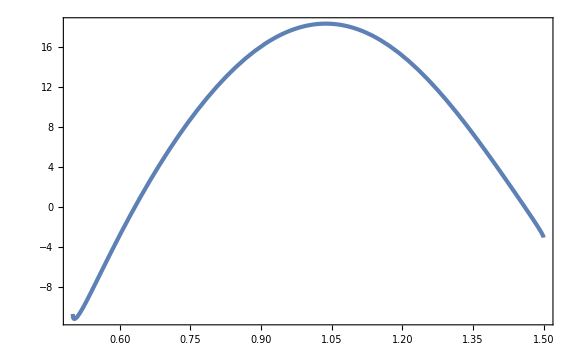

```mathematica
Plot[PcIntegrand[1/2,q,0,π/3,2π/3],{q,1/2,3/2},PlotRange->Full]
```

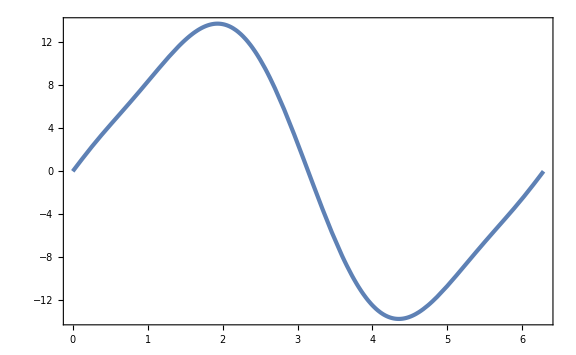

```mathematica
Plot[PcIntegrand[1/2,1,-1/2,p3,2π/3],{p3,0,2π},PlotRange->Full]
```

```mathematica
OGWp[k_]:=2/π^2 k^2 NIntegrate[PpIntegrand[k,q,c3,p3,p2],{q,Abs[k-1],Min[2,k+1]},{c3,-1,1},{p3,0,2π},{p2,0,2π}]
OGWc[k_]:=2/π^2 k^2 NIntegrate[PcIntegrand[k,q,c3,p3,p2],{q,Abs[k-1],Min[2,k+1]},{c3,-1,1},{p3,0,2π},{p2,0,2π},Method->"MonteCarlo"]
```

```mathematica
OGWp[1/2]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -30.4828 and 0.234274 for the integral and error estimates.

{13.3799,-1.54428}